```mathematica
generalContainerLike = (1-(1-p)^entrysize)^entriesIntercept((1-p)^entrysize)^(entriesTotal-entriesIntercept)
generalContainerLogLike=Log[generalContainerLike]
```

(1-(1-p)^entrysize)^entriesIntercept ((1-p)^entrysize)^(-entriesIntercept+entriesTotal)

Log[(1-(1-p)^entrysize)^entriesIntercept ((1-p)^entrysize)^(-entriesIntercept+entriesTotal)]

```mathematica
FIMgeneralContainer=-D[D[generalContainerLogLike,p]//FullSimplify,p]//FullSimplify
```

(entrysize (entriesTotal+(entriesIntercept (-1+(1+entrysize) (1-p)^entrysize))/((-1+(1-p)^entrysize)^2)))/(-1+p)^2

```mathematica
FIMgeneralContainer/.entrysize->s/.entriesTotal->n/.entriesIntercept->i
```

(s (n+(i (-1+(1-p)^s (1+s)))/((-1+(1-p)^s)^2)))/(-1+p)^2

```mathematica
FIMgeneralContainer/.entriesIntercept-> entriesTotal*(1-(1-p)^entrysize)//FullSimplify
```

-(entriesTotal entrysize^2 (1-p)^(-2+entrysize))/(-1+(1-p)^entrysize)

```mathematica
FIMgeneralContainer/.entriesIntercept-> entriesTotal*(1-(1-p)^entrysize)/.entrysize->s/.entriesTotal->n/.entriesIntercept->i//FullSimplify
```

-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)

```mathematica
SECombined=Sqrt[1/FIMgeneralContainer]/.entriesIntercept-> entriesTotal*(1-(1-p)^entrysize)//FullSimplify
```

√(-((-1+(1-p)^entrysize) (1-p)^(2-entrysize))/(entriesTotal entrysize^2))

```mathematica
SECombined/.entrysize->s/.entriesTotal->n/.entriesIntercept->i//FullSimplify
```

√(-((-1+(1-p)^s) (1-p)^(2-s))/(n s^2))

```mathematica
SECombined/.entrysize->s/.entriesTotal->n/.entriesIntercept->i//FullSimplify
```

√(-((-1+(1-p)^s) (1-p)^(2-s))/(n s^2))

```mathematica
√(-((-1+(1-p)^s) (1-p)^(2-s))/(n s^2))/.n->5/.p->.1/.s->1
```

0.134164

```mathematica
√(-((-1+(1-p)^s) (1-p)^(2-s))/(n s^2))
```

```mathematica
-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)/.n->200/.p->.5/.s->2
```

1066.67

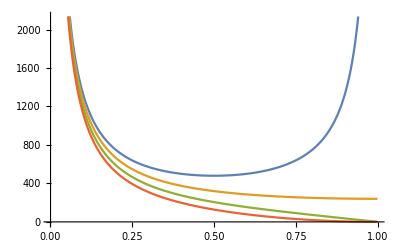

```mathematica
Plot[{-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)/.s->1/.n->120, -(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)/.s->2/.n->60,-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)/.s->3/.n->40,-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s)/.s->4/.n->30},{p,0.001,0.999}]
```

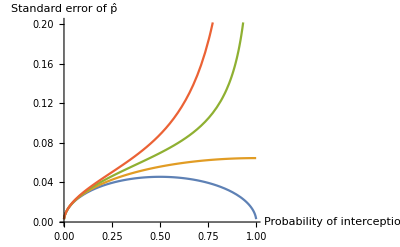

```mathematica
Plot[{Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->1/.n->120, Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->2/.n->60,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->3/.n->40,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->4/.n->30},{p,0.001,0.999},AxesLabel->{"Probability of interception","Standard error of p̂"}]
```

```mathematica
OverHat[p]
```

p̂

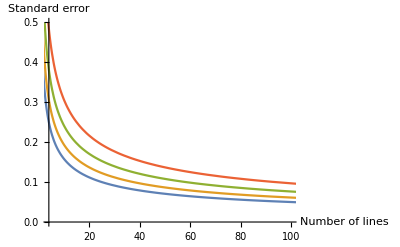

```mathematica
Plot[{Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->1/.n->nn/.p->.5, Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->2/.n->nn/2/.p->.5,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->3/.n->nn/3/.p->.5,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->4/.n->nn/4/.p->.5},{nn,1,500}, PlotRange->{{4,100},{0,.5}},AxesLabel->{"Number of lines","Standard error"}]
```

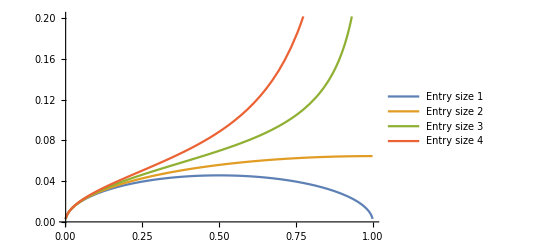
-Graphics-Standard error of p̂Probability of non-compliance

```mathematica
plot1=Labeled[Labeled[Plot[{Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->1/.n->120, Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->2/.n->60,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->3/.n->40,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->4/.n->30},{p,0.001,0.999}, PlotLegends->Placed[{"Entry size 1","Entry size 2","Entry size 3","Entry size 4"},{Left,Top}]],Text@TraditionalForm@Style["Standard error of p̂",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Probability of non-compliance",16]]
```

```mathematica
SetDirectory["C:\Users\cbaker1\Dropbox\Botany\CEBRA\Projects\container-line-analysis-public\asymptotic_approximation"]
```

C:\Users\cbaker1\Dropbox\Botany\CEBRA\Projects\container-line-analysis-public\asymptotic_approximation

```mathematica
Directory[]
```

C:\Users\cbaker1\Dropbox\Botany\CEBRA\Projects\container-line-analysis-public\asymptotic_approximation

```mathematica
Export["SE_vs_pr_intercept.pdf",plot1]
```

SE_vs_pr_intercept.pdf

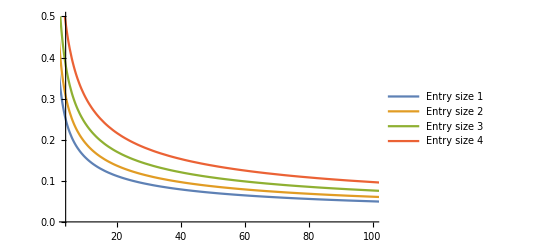
-Graphics-Standard error of p̂Number of lines

```mathematica
plot2=Labeled[Labeled[Plot[{Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->1/.n->nn/.p->.5, Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->2/.n->nn/2/.p->.5,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->3/.n->nn/3/.p->.5,Sqrt[1/(-(n (1-p)^(-2+s) s^2)/(-1+(1-p)^s))]/.s->4/.n->nn/4/.p->.5},{nn,1,500},  PlotRange->{{4,100},{0,.5}},PlotLegends->Placed[{"Entry size 1","Entry size 2","Entry size 3","Entry size 4"},{Right,Top}]] ,Text@TraditionalForm@Style["Standard error of p̂",16],Left,RotateLabel->True],Text@TraditionalForm@Style["Number of lines",16]]
```

```mathematica
Export["SE_vs_num_lines.pdf",plot2]
```

SE_vs_num_lines.pdf